### Meta Images

#### Avatar

```mathematica
Graphics[{Circle[],Text[Style["E",24,Bold,FontFamily->"Helvetica"],{0,-0.25}]},ImageSize->30]
```

-Graphics-

```mathematica
Graphics[{Circle[],Text[Style["尤",24,Bold,FontFamily->"Helvetica"],{0,0}]},ImageSize->30]
```

-Graphics-

```mathematica
Graphics[{{Black,Rectangle[{-1,-1},{1,1},RoundingRadius->0.4]},{White,AbsoluteThickness[2.5],Circle[{0,0},0.75]},{White,Text[Style["E",18,Bold,FontFamily->"Helvetica"],{0,-0.1}]}},ImageSize->30]
```

-Graphics-

```mathematica
Graphics[{{Red,Rectangle[{-1,-1},{1,1},RoundingRadius->0.4]},{White,AbsoluteThickness[2.5],Circle[{0,0},0.75]},{White,Text[Style["E",18,Bold,FontFamily->"Helvetica"],{0,-0.1}]}},ImageSize->30]
```

-Graphics-

```mathematica
Graphics[{{LightGray,Rectangle[{-1,-1},{1,1},RoundingRadius->0.4]},{Black,AbsoluteThickness[2.5],Circle[{0,0},0.75]},{Black,Text[Style["E",18,Bold,FontFamily->"Helvetica"],{0,-0.1}]}},ImageSize->30]
```

-Graphics-

```mathematica
Graphics[{{Black,Rectangle[{-1,-1},{1,1},RoundingRadius->0.4]},{EdgeForm[Directive[White,AbsoluteThickness[2]]],Black,Rectangle[{-0.8,-0.8},{0.8,0.8},RoundingRadius->0.2]},{White,Text[Style["E",20,Bold,FontFamily->"Helvetica"],{0,-0.2}]}},ImageSize->30]
```

-Graphics-

```mathematica
Graphics[{{Red,Rectangle[{-1,-1},{1,1},RoundingRadius->0.4]},{EdgeForm[Directive[White,AbsoluteThickness[2]]],Red,Rectangle[{-0.8,-0.8},{0.8,0.8},RoundingRadius->0.2]},{White,Text[Style["E",20,Bold,FontFamily->"Helvetica"],{0,-0.2}]}},ImageSize->30]
```

-Graphics-

## Posts

### AI for QEC

#### QEC

```mathematica
Block[{gate,meter,anc,bot},
gate[{i_,j_},l_,col_:Red]:={EdgeForm[Black],Lighter[col,0.8],Rectangle[{l-0.35,i-0.35},{l+0.35,j+0.35},RoundingRadius->.2]};
meter=Block[{th=1.2,a=0.35},{{EdgeForm[AbsoluteThickness[th]],Lighter[Orange,0.8],Rectangle[{0,-a},{2a,a},RoundingRadius->0.01]},{AbsoluteThickness[th],Circle[{a,-1.5a},a Sqrt[2],{π/4,3π/4}],Line[{#,Interpolation[{{a,-1.5a},{2a,a}},#,InterpolationOrder->1]}&/@{1.3a,1.8a}]}}];
anc={EdgeForm[Black],Lighter[Yellow,0.8],Triangle[{{0,0.4},{0,-0.4},{-0.5,0}}]};
bot=Block[{th=1.2,a=0.8,b=0.6,c=0.15,(*d=1.1,*)e=0.2,h=0.3,rr=0.3,re=0.25,ry=0.15,dy=0.3,nw=0.2,nh=0.2},{{EdgeForm[Directive[Black,AbsoluteThickness[th]]],White,Disk[{#,0},re]&/@{-a,a},Translate[Rectangle[{-nw,-nh},{nw,nh}],{0,-b-nh}],Rectangle[{-a,-b},{a,b},RoundingRadius->rr],Rectangle[{-a+c,-b+c},{a-c,b-c},RoundingRadius->(1-c/a)rr],Disk[{#,0},ry]&/@{-dy,dy},Translate[{(*{Black,AbsoluteThickness[th],Line[{#,0}&/@{-d,d}],Scale[Translate[Circle[{e,0},e,{π/2,3π/2}],{d,0}],{#,1},{0,0}]&/@{1,-1}},*)Rectangle[{-a,-h},{a,h}]},{0,-b-nh-h}]}}];
Graphics[{{Dashed,LightGray,AbsoluteThickness[1],Line[{#,0}&/@{-1,21}]},
Block[{ah},
ah[x_:0.5]:=Directive[Arrowheads[{{0.001,x,Graphics[Line[Offset/@{{-2,3},{2,0},{-2,-3}}]]}}],AbsoluteThickness[2]];Translate[{{ah[],Arrow[{#,-1.1}&/@{2,3}],Translate[{Arrow[{#,0}&/@{5,8}],Text[Style["memory","SansText"],{6.5,0},{0,1}]},{5#,-1.1}]&/@Range[0,2]},Translate[{{ah[],
{Orange,Arrow@BSplineCurve[{{-0.6,1.5},{-0.6,1.2},{-0.3,1},{-0.3,0.7}}]},{Green,Arrow[{{0,0.7},{0,<|0->3.5,1->5.5,2->4.5,3->3.5|>[#]}}]},If[#<3,{Blue,Arrow@BSplineCurve[{{1.2,0},{2,0},{2,1},{2,1.5}}]},Nothing]},bot},{4+5#,0}]&/@Range[0,3]},{0,-1}]],
Text[Style["Quantum Circuit",Bold,"SansText"],{10,6}],Text[Style["AI Decoder",Bold,"SansText"],{10,-3.5}],
Translate[{{EdgeForm[Black],White,Rectangle[{-1.35,-1.5},{1.35,1.5}]},Text[Style["Prompt:\nCode\nDevice\n...",12,"SansText",LineSpacing->{0,12}]]},{0.5,-2}],{Translate[Line[{#,0}&/@{0,20}],{0,#}]&/@Range[3,5],Translate[Translate[{Translate[anc,{0,0}],Line[{#,0}&/@{0,3}],Translate[meter,{3,0}]},{0,#}]&/@{1,2},{5#,0}]&/@Range[0,3]},
{gate[{5,5},1],gate[{3,5},2],gate[{4,5},3],gate[{3,3},5],gate[{4,4},5],gate[{4,5},6],gate[{3,4},7],gate[{4,5},8],gate[{4,5},8],gate[{3,3},10],gate[{4,5},10],gate[{5,5},11],gate[{3,4},11],gate[{4,4},12],gate[{3,4},13],gate[{3,3},15],gate[{5,5},15],gate[{4,5},16],gate[{4,4},17],gate[{4,5},18]},{gate[{2,3},1,#],gate[{1,2},2,#],gate[{1,3},6,#],gate[{2,2},7,#],gate[{1,2},11,#],gate[{2,3},12,#],gate[{2,3},16,#],gate[{1,3},17,#]}&@Blue,{gate[{3,4},4,Green],gate[{5,5},9,Green],gate[{4,5},14,Green],gate[{3,3},19,Green],gate[{4,5},19,Green]}},Background->RGBColor["#FFF9D0"],ImageSize->420]]
```

-Graphics-

```mathematica
Block[{gate,meter,anc,bot},
gate[{i_,j_},l_,col_:Red]:={EdgeForm[Black],Lighter[col,0.8],Rectangle[{l-0.35,i-0.35},{l+0.35,j+0.35},RoundingRadius->.2]};
meter=Block[{th=1.2,a=0.35},{{EdgeForm[AbsoluteThickness[th]],Lighter[Orange,0.8],Rectangle[{0,-a},{2a,a},RoundingRadius->0.01]},{AbsoluteThickness[th],Circle[{a,-1.5a},a Sqrt[2],{π/4,3π/4}],Line[{#,Interpolation[{{a,-1.5a},{2a,a}},#,InterpolationOrder->1]}&/@{1.3a,1.8a}]}}];
anc={EdgeForm[Black],Lighter[Yellow,0.8],Triangle[{{0,0.4},{0,-0.4},{-0.5,0}}]};
bot=Block[{th=1.2,a=0.8,b=0.6,c=0.15,(*d=1.1,*)e=0.2,h=0.3,rr=0.3,re=0.25,ry=0.15,dy=0.3,nw=0.2,nh=0.2},{{EdgeForm[Directive[Black,AbsoluteThickness[th]]],White,Disk[{#,0},re]&/@{-a,a},Translate[Rectangle[{-nw,-nh},{nw,nh}],{0,-b-nh}],Rectangle[{-a,-b},{a,b},RoundingRadius->rr],Rectangle[{-a+c,-b+c},{a-c,b-c},RoundingRadius->(1-c/a)rr],Disk[{#,0},ry]&/@{-dy,dy},Translate[{(*{Black,AbsoluteThickness[th],Line[{#,0}&/@{-d,d}],Scale[Translate[Circle[{e,0},e,{π/2,3π/2}],{d,0}],{#,1},{0,0}]&/@{1,-1}},*)Rectangle[{-a,-h},{a,h}]},{0,-b-nh-h}]}}];
Graphics[{{Dashed,LightGray,AbsoluteThickness[1],Line[{#,0}&/@{-1,21}]},
Block[{ah},
ah[x_:0.5]:=Directive[Arrowheads[{{0.001,x,Graphics[Line[Offset/@{{-2,3},{2,0},{-2,-3}}]]}}],AbsoluteThickness[2]];Translate[{{ah[],Arrow[{#,-1.1}&/@{2,3}],Translate[{Arrow[{#,0}&/@{5,8}],Text[Style["memory","SansText"],{6.5,0},{0,1}]},{5#,-1.1}]&/@Range[0,2]},Translate[{{ah[],
{Orange,Arrow@BSplineCurve[{{-0.6,1.5},{-0.6,1.2},{-0.3,1},{-0.3,0.7}}]},{Green,Arrow[{{0,0.7},{0,<|0->3.5,1->5.5,2->4.5,3->3.5|>[#]}}]},If[#<3,{Blue,Arrow@BSplineCurve[{{1.2,0},{2,0},{2,1},{2,1.5}}]},Nothing]},bot},{4+5#,0}]&/@Range[0,3]},{0,-1}]],
Translate[{{EdgeForm[Black],White,Rectangle[{-1.35,-1.5},{1.35,1.5}]},Text[Style["Prompt:\nCode\nDevice\n...",12,"SansText",LineSpacing->{0,12}]]},{0.5,-2}],{Translate[Line[{#,0}&/@{0,20}],{0,#}]&/@Range[3,5],Translate[Translate[{Translate[anc,{0,0}],Line[{#,0}&/@{0,3}],Translate[meter,{3,0}]},{0,#}]&/@{1,2},{5#,0}]&/@Range[0,3]},
{gate[{5,5},1],gate[{3,5},2],gate[{4,5},3],gate[{3,3},5],gate[{4,4},5],gate[{4,5},6],gate[{3,4},7],gate[{4,5},8],gate[{4,5},8],gate[{3,3},10],gate[{4,5},10],gate[{5,5},11],gate[{3,4},11],gate[{4,4},12],gate[{3,4},13],gate[{3,3},15],gate[{5,5},15],gate[{4,5},16],gate[{4,4},17],gate[{4,5},18]},{gate[{2,3},1,#],gate[{1,2},2,#],gate[{1,3},6,#],gate[{2,2},7,#],gate[{1,2},11,#],gate[{2,3},12,#],gate[{2,3},16,#],gate[{1,3},17,#]}&@Blue,{gate[{3,4},4,Green],gate[{5,5},9,Green],gate[{4,5},14,Green],gate[{3,3},19,Green],gate[{4,5},19,Green]}},Background->RGBColor["#FFF9D0"],PlotRange->{{-6,26},All},ImageSize->560]]
```

-Graphics-

#### Error Propagation

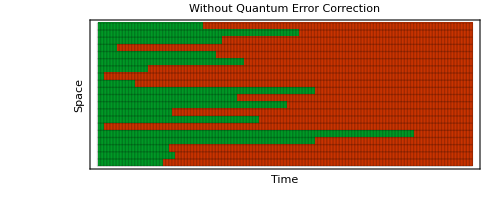
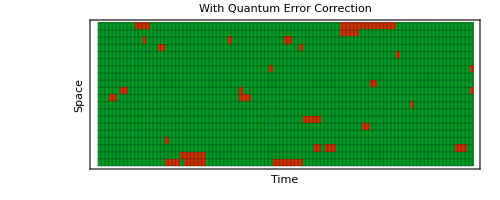
-Graphics-
-Graphics-
-Graphics--Graphics-

```mathematica
Block[{p1=0.01,p2=0.01,r=0.3,bits,auto},
bits=ConstantArray[0,20];
auto[m_,map_][input_]:=Block[{state=input,n},
n=Length[state];
Do[state[[i;;i+m-1]]=map[state[[i;;i+m-1]]],{i,1,n-m+1}];
state];
SeedRandom[8];
Style[Column[{ArrayPlot[Transpose@NestList[Composition[auto[2,<|{0,0}:>{0,0},{0,1}:>RandomChoice[{1-p2,p2}->{{0,1},{1,1}}],{1,0}:>RandomChoice[{1-p2,p2}->{{1,0},{1,1}}],{1,1}:>{1,1}|>],auto[1,<|{0}:>RandomChoice[{1-p1,p1}->{{0},{1}}],{1}:>{1}|>]],bits,120],ColorRules->{0->Green,1->Red},Mesh->All,MeshStyle->Directive[Opacity[0.2],AbsoluteThickness[1]],PlotRangePadding->0,Frame->True,FrameLabel->{"Space","Time"},PlotLabel->"Without Quantum Error Correction",ImageSize->500],
ArrayPlot[Transpose@NestList[Composition[auto[2,<|{0,0}:>{0,0},{0,1}:>RandomChoice[{1-p2,p2}->{{0,1},{1,1}}],{1,0}:>RandomChoice[{1-p2,p2}->{{1,0},{1,1}}],{1,1}:>{1,1}|>],auto[1,<|{0}:>RandomChoice[{1-p1,p1}->{{0},{1}}],{1}:>RandomChoice[{1-r,r}->{1,0}]|>]],bits,100],ColorRules->{0->Green,1->Red},Mesh->All,MeshStyle->Directive[Opacity[0.2],AbsoluteThickness[1]],PlotRangePadding->0,Frame->True,FrameLabel->{"Space","Time"},PlotLabel->"With Quantum Error Correction",ImageSize->500],
Row[Graphics[{{EdgeForm[AbsoluteThickness[1]],#1,Rectangle[Offset@{-3,-3},Offset@{3,3}]},Text[#2,{1,0},{-1.2,0.15}]},ImageSize->{Automatic,14}]&@@@Thread@{{Green,Red},{"Correct","Error"}},Spacer[20]]},Alignment->Center],Background->RGBColor["#FFF9D0"]]
]
```